```mathematica
Solve[{5x^2+6y^2+z==9,x+y==1},{x,y}]
```

{{x→1/11 (6-√(69-11 z)),y→1/11 (5+√(69-11 z))},{x→6/11+1/11 √(69-11 z),y→1/11 (5-√(69-11 z))}}

```mathematica
Solve[{x+y+z==9,x+4*y==4,2*x+3*y+z==9},{x,y,z}]
```

{{x→-4,y→2,z→11}}

```mathematica
FindRoot[Log[x]-Sin[x]-2==0,{x,4}]
```

{x→3.85128}

```mathematica
FindRoot[{Sin[x *y]==Sin[x *y]+Cos[y],Cos[x* y]==Sin[x]+Cos[y]},{x,0.6},{y,1.4}]
```

{x→0.611015,y→1.5708}

```mathematica
Problem Sheet 4(2d)
```

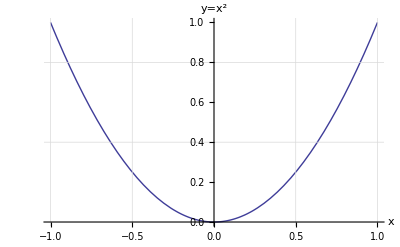

Plot::optrs: "Option specification {x, -1, 1}\\\ AxesLabel → {\"<x>\", \"\\\"<y=\!\(\*SuperscriptBox[\(x\), \(2\)]\)>\\\"\"} in x^2 is not a rule for a symbol or string. (*ButtonBox[

Plot::nonopt: "Options expected (instead of Grid) beyond position 2 in Plot[SuperscriptBox[x, 2], {x, -1, 1}\\\ AxesLabel → {\"<x>\", \"\\\"<y=\!\(\*SuperscriptBox[\(x\), \(2\)]\)>\\\"\"}, Grid]. An option must be a rule or a list of rules. (*ButtonBox[

```mathematica
Plot[x^2,{x,-1,1},AxesLabel->{"x","y=x^2"},GridLines->{{-1,-0.5,0.5,1},{0.4,0.8}}]
```

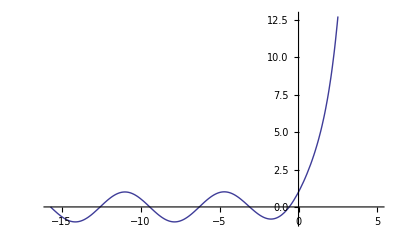

```mathematica
Plot[ⅇ^x+Sin[x],{x,-5π,5}]
```

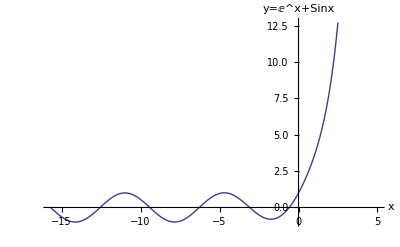

```mathematica
Plot[ⅇ^x+Sin[x],{x,-5π,5},AxesLabel->{"x","y=ⅇ^x+Sinx"},GridLines->{{-5π,-4π,-3π,-2π,-π,0,π,2π},{-1,0,1,2,3,4}}]
```

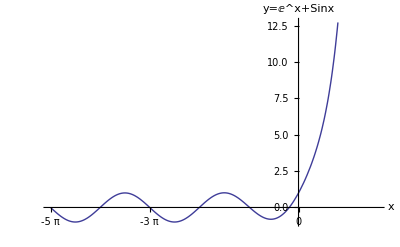

```mathematica
Plot[ⅇ^x+Sin[x],{x,-5π,5},AxesLabel->{"x","y=ⅇ^x+Sinx"},GridLines->{{-5π,-4π,-3π,-2π,-π,0,π,2π},{-1,0,1,2,3,4}},Ticks->{{-5π,-4π,-3π,-2π,0,π,2π},Automatic}]
```

Graphics::gprim: Silver was encountered where a Graphics primitive or directive was expected.

Graphics::gprim: RoyalBlue was encountered where a Graphics primitive or directive was expected.

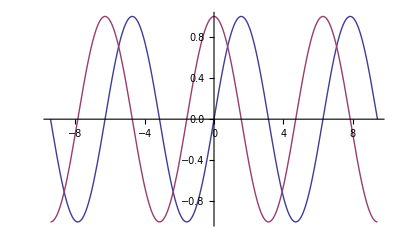

```mathematica
Plot[{Sin[x],Cos[x]},{x,-3π,3π},PlotStyle->{Silver,RoyalBlue}]
```

```mathematica
Plot[{Sin[x],Cos[x]},{x,-3π,3π},PlotStyle->{Silver,RoyalBlue},"PlotLegends`"->{"y=Sinx","y=Cosx"}]
```

Plot::optx: Unknown option "PlotLegends`" in Plot[{Sin[x], Cos[x]}, {x, -3\ π, 3\ π}, PlotStyle → {Silver, RoyalBlue}, "PlotLegends`" → {"y=Sinx", "y=Cosx"}].

Plot[{Sin[x],Cos[x]},{x,-3 π,3 π},PlotStyle→{Silver,RoyalBlue},PlotLegends`→{y=Sinx,y=Cosx}]

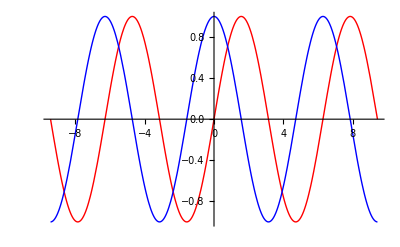

```mathematica
<<"PlotLegends`"
Plot[{Sin[x],Cos[x]},{x,-3π,3π},PlotStyle->{Red,Blue},PlotLegend->{"y=Sinx","y=Cosx"}]
```